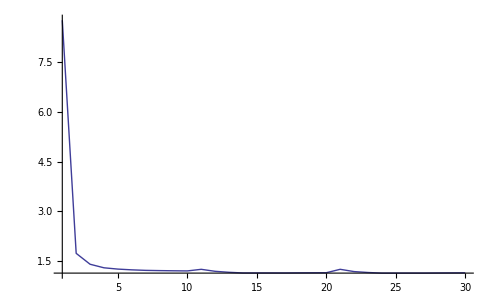

```mathematica
perplecity = {};
For[i=1,i≤3,i++,
data = Import["C:\\Users\\PhycauseStudio\\Documents\\GitHub\\Fianl_Project\\results\\hidden_size = 10 vocab_size = 100\\perplexity_log_Epoch"<>IntegerString[i]<>".txt"]]
perplecity = Join[perplecity , StringSplit[data]];
perplecities  = ToExpression[perplecity];
ListPlot[perplecities  ,PlotRange->All,Joined->True,PlotStyle->{Thick,PointSize[Large]}]
```